## Parametri e Variabili:

```mathematica
(*Parametri Modello*)
b1 = 2;
b2 = 2;
alfa1 = 1;
alfa2 = 1;
alfa3 = 1;
sigma = 1;

(*Numero di spin = numero di popolazioni*)
Nspin=300;
(*Numero di iterazioni e passo iterativo*)
Niter=50000;
dt=0.01 ;(*così è ordine 1 *)
```

## Condizioni iniziali:

```mathematica
X=RandomVariate[NormalDistribution[],Nspin];
MediaX=Table[Total[X]/Nspin, {iy,1,Niter}];
MediaX[[1]]

eps = 0; (* se vuoi un bias nella magnetizzazione iniziale *)
(*m = Table[RandomReal[{-1+eps,1}], {im, 1, Nspin}];*)
m = Table[1,{im,1,Nspin}];

m1 = Table[1, {im,1,Niter}]; (* la prima magnetizzazione *)
m2 = Table[1, {im,1,Niter}]; (* la seconda magnetizzazione *)

M = Table[Total[m]/Nspin,{iy,1,Niter}]; (* la magnetizzazione totale *)

M[[1]]

(* vorremmo inserire anche un dato non zero, almeno per la M *)
```

-0.0372317

1

## Simulazioni Sistema Stocastico:

```mathematica
For[i=1,i≤Niter-1, i++,
M[[i]]=Total[m]/Nspin;
m1[[i]] = m[[1]];
m2[[i]] = m[[2]];


U1 = RandomVariate[UniformDistribution[],Nspin];
U2 = RandomVariate[UniformDistribution[],Nspin];

W1=Boole[Table[Nspin*(1 + m[[j]])/2*Exp[-b1*m[[j]] - b2*M[[i]] - b1*X[[j]]]*dt>U1[[j]],{j,1,Nspin}]];
W2=Boole[Table[Nspin*(1 - m[[j]])/2*Exp[b1*m[[j]] + b2*M[[i]] + b1*X[[j]]]*dt>U2[[j]],{j,1,Nspin}]];
m = m - W1*(2/Nspin) + W2*(2/Nspin);
];
```

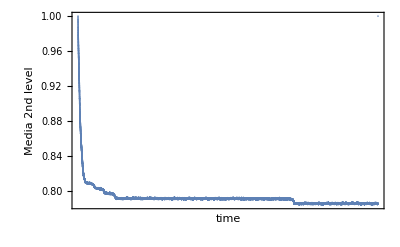

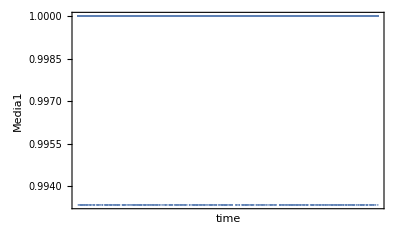

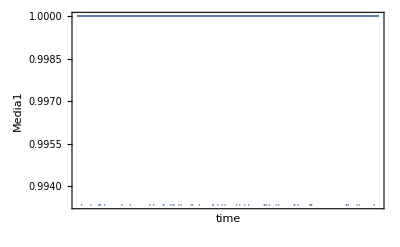

```mathematica
A=ListPlot[M,Frame->True,Axes->False,FrameLabel->{"time","Media 2nd level"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]

B =ListPlot[m1,Frame->True,Axes->False,FrameLabel->{"time","Media1"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]

L = ListPlot[m2,Frame->True,Axes->False,FrameLabel->{"time","Media1"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```